# Random Questions #1

## Which glass is closest to half-full?

Question from Presh Talwalkar on Instagram, linked here: https://www.instagram.com/p/C7XUdNkuxjU/?igsh=OGZwYm85bWhtaTVy

-Graphics-

## Solution:

To solve this, we need to use the following equation(s):

where r is the radius and h is the height  of the cone.

Let’s let the entire cone-shaped glass have a radius  and height . Then the fractional cone comprised of the liquid has a radius and height . We want to know which glass is closest to half-full, or rather, which fractional cone’s volume is equal to half of the entire cone’s volume. Which means, we wish to solve the following equation:

Using similar triangles from the cross-section of the cone, we can find the following relationship:

```mathematica
fullConeCrossSection = Triangle[{{0,0},{0,1},{-1,1}}];
fractionalConeCrossSection = Triangle[{{1,0},{1,0.5},{0.5,0.5}}];
Show[Graphics[{FaceForm[White],EdgeForm[Directive[Thick,Black]],EdgeLabels->{1<->2->"Hey"},fullConeCrossSection}],Graphics[{FaceForm[White],EdgeForm[Directive[Thick,Black]],fractionalConeCrossSection}]]
```

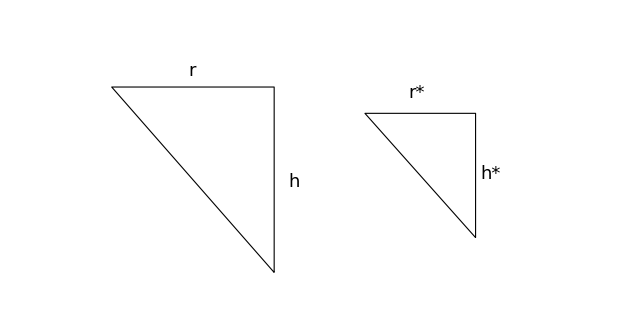

Now we can use Mathematica to solve this problem:

```mathematica
VCone=1/3 π r^2 h;
eq=1/2 VCone==1/3 π rs^2 hs;
```

```mathematica
rs=(hs r)/h; 
eq
```

1/6 h π r^2==(hs^3 π r^2)/(3 h^2)

Now we have an equation in terms of , , , and physical constants, where technically h and r should already be known. However, we know from the question stem the following equation:

where f is the fraction of the original height in decimal form (for example, 60% height as shown in the question/image would equate to an f value of 0.60).

```mathematica
hs=f h;
eq
```

1/6 h π r^2==1/3 f^3 h π r^2

```mathematica
eq=FullSimplify[eq,{r>0,h>0}]
```

2 f^3==1

```mathematica
NSolve[eq,f, Reals]
```

{{f→0.793701}}

From this, we can see that the exact fractional height that makes the glass half-full would be , or for the purposes of this question, , meaning that the solution to this question is “80% height”. We can confirm this by testing the volumes using the values .

```mathematica
N[1/6 π (1)^2 (1)]
N[1/3 π (0.8)^2 (0.8)]
```

0.523599

0.536165

Or if we use the exact value of f:

```mathematica
N[1/6 π (1)^2 (1)]
N[1/3 π (0.793701)^2 (0.793701)]
```

0.523599

0.5236

Solving the exact equation above yields the exact solution for f of